# Brendan Philbin Simple Ising Model Trials

## Trial 1: N = 4, M = 100, β = 0.1, J = +1, J_seed = 3, MC_seed = 5, Spins_seed = 1

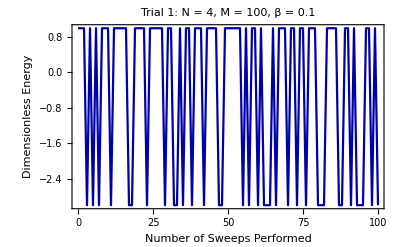

```mathematica
numSweeps=Range[0,100];
SetDirectory[NotebookDirectory[]];

trial1=Flatten[Import["ising_output1.csv","CSV"]];
trial1data=Transpose[{numSweeps,trial1}];
trial1plot=ListLinePlot[trial1data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 1: N = 4, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 2: N = 4, M = 100, β = 1, J = +1, J_seed = 3, MC_seed = 6, Spins_seed = 2

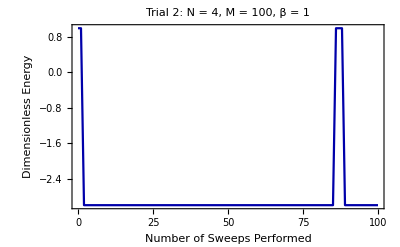

```mathematica
trial2=Flatten[Import["ising_output2.csv","CSV"]];
trial2data=Transpose[{numSweeps,trial2}];
trial2plot=ListLinePlot[trial2data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 2: N = 4, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 3: N = 4, M = 100, β = 10, J = +1, J_seed = 3, MC_seed = 7, Spins_seed = 3

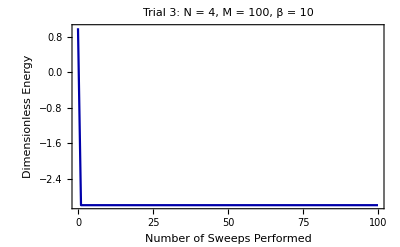

```mathematica
trial3=Flatten[Import["ising_output3.csv","CSV"]];
trial3data=Transpose[{numSweeps,trial3}];
trial3plot=ListLinePlot[trial3data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 3: N = 4, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 4: N = 16, M = 100, β = 0.1, J = +1, J_seed = 4, MC_seed = 8, Spins_seed = 4

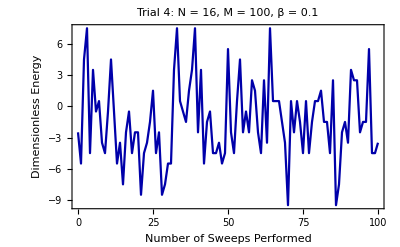

```mathematica
trial4=Flatten[Import["ising_output4.csv","CSV"]];
trial4data=Transpose[{numSweeps,trial4}];
trial4plot=ListLinePlot[trial4data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 4: N = 16, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 5: N = 16, M = 100, β = 1, J = +1, J_seed = 4, MC_seed = 9, Spins_seed = 5

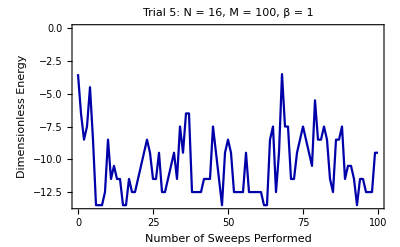

```mathematica
trial5=Flatten[Import["ising_output5.csv","CSV"]];
trial5data=Transpose[{numSweeps,trial5}];
trial5plot=ListLinePlot[trial5data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 5: N = 16, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 6: N = 16, M = 100, β = 10, J = +1, J_seed = 4, MC_seed = 10, Spins_seed = 6

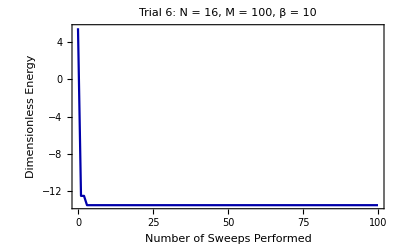

```mathematica
trial6=Flatten[Import["ising_output6.csv","CSV"]];
trial6data=Transpose[{numSweeps,trial6}];
trial6plot=ListLinePlot[trial6data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 6: N = 16, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 7: N = 64, M = 100, β = 0.1, J = +1, J_seed = 5, MC_seed = 11, Spins_seed = 7

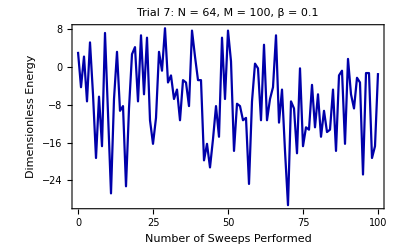

```mathematica
trial7=Flatten[Import["ising_output7.csv","CSV"]];
trial7data=Transpose[{numSweeps,trial7}];
trial7plot=ListLinePlot[trial7data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 7: N = 64, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 8: N = 64, M = 100, β = 1, J = +1, J_seed = 5, MC_seed = 12, Spins_seed = 8

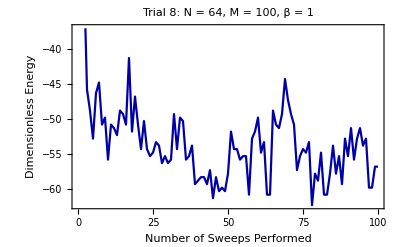

```mathematica
trial8=Flatten[Import["ising_output8.csv","CSV"]];
trial8data=Transpose[{numSweeps,trial8}];
trial8plot=ListLinePlot[trial8data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 8: N = 64, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 9: N = 64, M = 100, β = 10, J = +1, J_seed = 5, MC_seed = 13, Spins_seed = 9

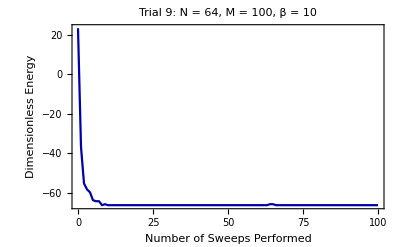

```mathematica
trial9=Flatten[Import["ising_output9.csv","CSV"]];
trial9data=Transpose[{numSweeps,trial9}];
trial9plot=ListLinePlot[trial9data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 9: N = 64, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 10: N = 8, M = 100, β = 0.1, J = +/-1, J_seed = 6, MC_seed = 14, Spins_seed = 10

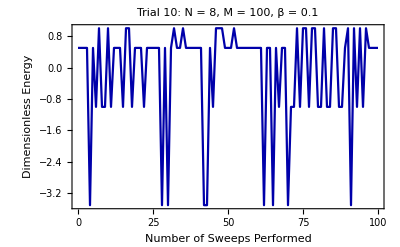

```mathematica
trial10=Flatten[Import["ising_output10.csv","CSV"]];
trial10data=Transpose[{numSweeps,trial10}];
trial10plot=ListLinePlot[trial10data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 10: N = 8, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 11: N = 8, M = 100, β = 1, J = +/-1, J_seed = 6, MC_seed = 15, Spins_seed = 11

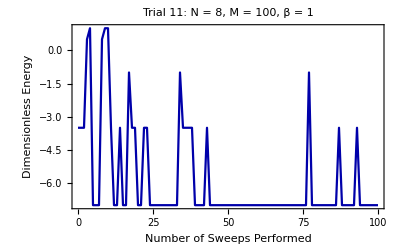

```mathematica
trial11=Flatten[Import["ising_output11.csv","CSV"]];
trial11data=Transpose[{numSweeps,trial11}];
trial11plot=ListLinePlot[trial11data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 11: N = 8, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 12: N = 8, M = 100, β = 10, J = +/-1, J_seed = 6, MC_seed = 16, Spins_seed = 12

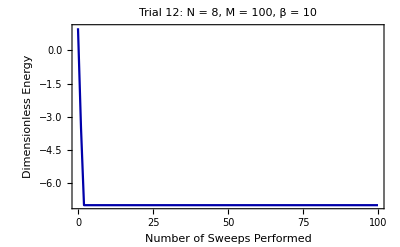

```mathematica
trial12=Flatten[Import["ising_output12.csv","CSV"]];
trial12data=Transpose[{numSweeps,trial12}];
trial12plot=ListLinePlot[trial12data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 12: N = 8, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 13: N = 16, M = 100, β = 0.1, J = +/-1, J_seed = 7, MC_seed = 17, Spins_seed = 13

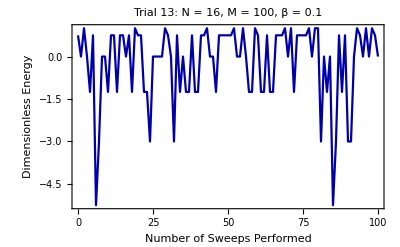

```mathematica
trial13=Flatten[Import["ising_output13.csv","CSV"]];
trial13data=Transpose[{numSweeps,trial13}];
trial13plot=ListLinePlot[trial13data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 13: N = 16, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 14: N = 16, M = 100, β = 1, J = +/-1, J_seed = 7, MC_seed = 18, Spins_seed = 14

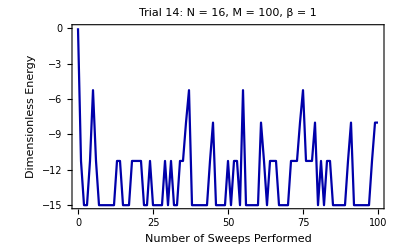

```mathematica
trial14=Flatten[Import["ising_output14.csv","CSV"]];
trial14data=Transpose[{numSweeps,trial14}];
trial14plot=ListLinePlot[trial14data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 14: N = 16, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 15: N = 16, M = 100, β = 10, J = +/-1, J_seed = 7, MC_seed = 1, Spins_seed = 15

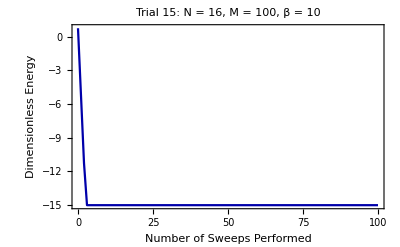

```mathematica
trial15=Flatten[Import["ising_output15.csv","CSV"]];
trial15data=Transpose[{numSweeps,trial15}];
trial15plot=ListLinePlot[trial15data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 15: N = 16, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 16: N = 32, M = 100, β = 0.1, J = +/-1, J_seed = 8, MC_seed = 20, Spins_seed = 16

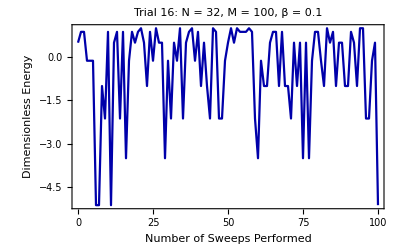

```mathematica
trial16=Flatten[Import["ising_output16.csv","CSV"]];
trial16data=Transpose[{numSweeps,trial16}];
trial16plot=ListLinePlot[trial16data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 16: N = 32, M = 100, β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 17: N = 32, M = 100, β = 1, J = +/-1, J_seed = 8, MC_seed = 21, Spins_seed = 17

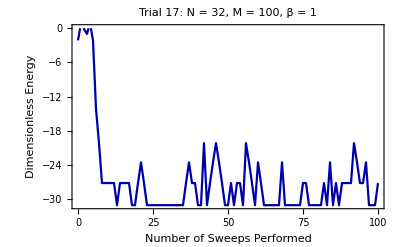

```mathematica
trial17=Flatten[Import["ising_output17.csv","CSV"]];
trial17data=Transpose[{numSweeps,trial17}];
trial17plot=ListLinePlot[trial17data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 17: N = 32, M = 100, β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```

## Trial 18: N = 32, M = 100, β = 10, J = +/-1, J_seed = 8, MC_seed = 22, Spins_seed = 17

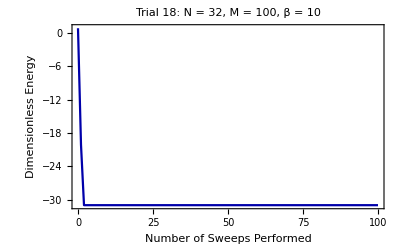

```mathematica
trial18=Flatten[Import["ising_output18.csv","CSV"]];
trial18data=Transpose[{numSweeps,trial18}];
trial18plot=ListLinePlot[trial18data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"Trial 18: N = 32, M = 100, β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```